```mathematica
(* Generating function for model X (->)^k1 Y+Z, Y (->)^k2 X *)
```

```mathematica
exponent=x10((MatrixExp[-({{k1, -k1 sz}, {-k2, k2}})t].({{sx}, {sy}}))[[1]][[1]]-1)+x20((MatrixExp[-({{k1, -k1 sz}, {-k2, k2}})t].({{sx}, {sy}}))[[2]][[1]]-1);
```

```mathematica
g[sx_,sy_,sz_,t_]:=Exp[x10((MatrixExp[-({{k1, -k1 sz}, {-k2, k2}})t].({{sx}, {sy}}))[[1]][[1]]-1)+x20((MatrixExp[-({{k1, -k1 sz}, {-k2, k2}})t].({{sx}, {sy}}))[[2]][[1]]-1)]
```

```mathematica
(* Maximual number of Z particles in plot *)
kmax=190;
(* Simulation time in seconds *)
τmax=20;
```

```mathematica
(* Coefficients of the compound Poisson distribution *)
```

```mathematica
(* α=Table[SeriesCoefficient[exponent/.sx->1/.sy->1/.{k1->{7.0},k2->{1.875},x10->{1.875},x20->{1.875},t->{τ}},{sz,0,n}],{n,0,50},{τ,0,τmax}]; *)
```

```mathematica
(* Save these coefficients to hard disk *)
```

```mathematica
(* Export[NotebookDirectory[]<>"alphamulti.dat",α] *)
```

/home/matze/Paper/code/alphamulti.dat

```mathematica
(* Import these coefficients from hard disk *)
```

```mathematica
α=Import[NotebookDirectory[]<>"alphamulti.dat","Table"];
```

```mathematica
α=ToExpression[α];
```

```mathematica
α=Abs[α];
```

```mathematica
(* Initial expected numbers of X and Y *)
```

```mathematica
x10=1.875;x20=1.875;
```

```mathematica
(* Levy-Adelson-Panjer Recursion *)
```

```mathematica
For[τ=1;p=ConstantArray[0,{kmax+1,τmax+1}],τ≤ τmax,τ++,For[k=0;p[[1]][[τ+1]]=ⅇ^(-x10-x20),k<kmax,k++,p[[k+1+1]][[τ+1]]=1/(k+1)∑_(j=0)^k N[(k+1-j)If[(k+1-j)<50,α[[(k+1-j)+1]][[τ+1]][[1]],0]p[[j+1]][[τ+1]]]]]
```

```mathematica
meantab=Table[ ∑_(k=0)^(kmax-1) p[[k+1]][[τ]]*k,{τ,2,13}]
```

{4.59876,11.3586,17.3656,23.0384,28.593,34.1379,39.6801,45.2217,50.7589,56.2713,61.7042,66.9625}

```mathematica
stdtab=Table[√( ∑_(k=0)^(kmax-1) p[[k+1]][[τ]]*k^2-∑_(k=0)^(kmax-1) p[[k+1]][[τ]]*k),{τ,2,13}]
```

{6.97475,13.1474,19.4985,25.8026,32.0328,38.2696,44.5066,50.7434,56.972,63.162,69.2438,75.1102}

```mathematica
α=Threshold[α];
```

```mathematica
origin=-3;
```

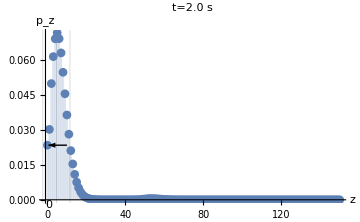
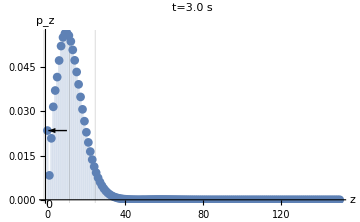
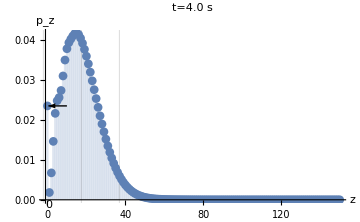
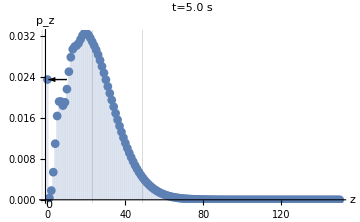
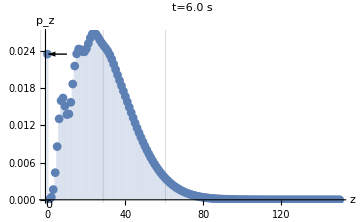
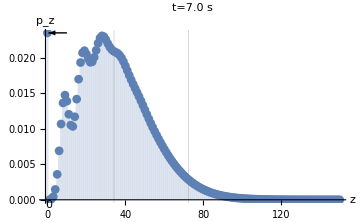
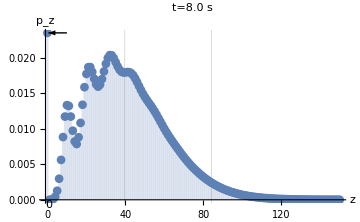
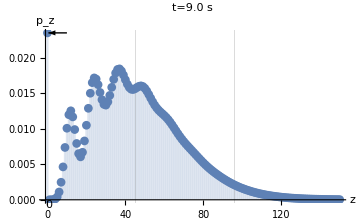

```mathematica
plots=Table[Show[DiscretePlot[p[[xk+1]][[τ]],{xk,0,150},GridLines->{{{meantab[[τ-1]],Thick},{meantab[[τ-1]]-stdtab[[τ-1]],{Dashed,Thick}},{meantab[[τ-1]]+stdtab[[τ-1]],{Dashed,Thick}}},None},AxesLabel->{"z","p_z"},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},AxesOrigin->{origin,0},PlotMarkers->Automatic,PlotLabel->"t="<>ToString[NumberForm[τ,{2,1}]]<>" s",Joined->False,Epilog->{Text[0,{origin,0},{origin,1.2}]}],Graphics[Arrow[{{10,p[[1]][[τ]]},{0.5,p[[1]][[τ]]}}]]],{τ,2,13}]
```

```mathematica
Length[plots]
```

12

```mathematica
For[τ=2,τ≤13,τ++,Export[NotebookDirectory[]<>"../bilder/splitting"<>ToString[τ]<>".pdf",plots[[τ-1]]]]
```

```mathematica
For[τ=2,τ≤13,τ++,plot=DiscretePlot[p[[xk+1]][[τ]],{xk,0,150},GridLines->{{{meantab[[τ-1]],Thick},{meantab[[τ-1]]-stdtab[[τ-1]],Dashed},{meantab[[τ-1]]+stdtab[[τ-1]],Dashed}},None},AxesLabel->{"k","p_k"},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},PlotLabel->"τ="<>ToString[NumberForm[τ,{2,1}]]<>" s"];Export[NotebookDirectory[]<>"splitting"<>ToString[τ]<>".pdf",plot]]
```

```mathematica
Table[DiscretePlot3D[SeriesCoefficient[g[sX,sY,1,t]/.{k1->{7.0},k2->{1.875},x10->{1.875},x20->{1.875}},{sX,0,kX},{sY,0,kY}],{kX,0,5},{kY,0,5},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},AxesLabel->{"x","y","p_(x, y)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[t*0.1,{2,1}]]<>" s"],{t,{2,10}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Table[DiscretePlot3D[SeriesCoefficient[g[sX,1,sZ,t]/.{k1->{7.0},k2->{1.875},x10->{1.875},x20->{1.875}},{sX,0,kX},{sZ,0,kZ}],{kX,0,5},{kZ,0,nmax},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},AxesLabel->{"x","z","p_(x, z)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[t*0.1,{2,1}]]<>" s"],{t,{2,10}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Table[SeriesCoefficient[g[sX,1,sZ,t]/.{k1->{7.0},k2->{1.875},x10->{1.875},x20->{1.875}},{sX,0,kX},{sZ,0,kZ}],{kX,0,5},{kZ,0,nmax},{t,{2,10}}]
```

{{{{0.024578},{0.0235177}},{{0.00648978},{8.39898×10^-9}},{{0.0164399},{1.06811×10^-7}},{{0.0243827},{8.69984×10^-7}},{{0.0269758},{5.10643×10^-6}},{{0.0278021},{0.0000230432}},{{0.0293732},{0.0000832963}},{{0.0306431},{0.000248158}},{{0.0305696},{0.000622256}},{{0.0294431},{0.00133454}},{{0.0278039},{0.00248006}},{{0.0258285},{0.00403352}},{{0.0235481},{0.00579888}},{{0.0210691},{0.00739838}},{{0.0185423},{0.00850495}},{{0.0160834},{0.00868903}},{{0.0137618},{0.00933233}},{{0.0116218},{0.00739826}},{{0.00969311},{0.00897223}},{{0.00799082},{-0.00443161}},{{0.00651564},{0.0570379}},{{0.0052577},{-0.212048}},{{0.0042006},{1.72588}},{{0.00332428},{1.98399}},{{0.00260704},{19.5587}},{{0.00202687},{23.6404}},{{0.0015629},{180.012}},{{0.00119549},{264.256}},{{0.000907659},{1010.91}},{{0.000684255},{1447.63}},{{0.000512704},{6053.87}},{{0.000380112},{2697.92}},{{0.000281665},{21555.8}},{{0.000195602},{-45641.2}},{{0.000141544},{-73986.3}},{{0.0000617289},{-358922.}},{{0.0000278109},{-742004.}},{{-0.0000201537},{-2.59022×10^6}},{{0.000113283},{-3.34559×10^6}},{{0.000376387},{-1.76806×10^7}},{{0.00176346},{-1.06217×10^7}},{{0.00199119},{-8.60714×10^7}},{{0.00931375},{-5.43607×10^7}},{{0.00657774},{-1.42054×10^8}},{{0.0320633},{-2.1908×10^7}},{{-0.00803992},{-5.00399×10^8}},{{0.0618225},{2.83105×10^9}},{{0.135634},{1.6184×10^9}},{{0.701946},{2.04962×10^10}},{{1.02872},{1.61065×10^10}},{{2.68054},{7.02627×10^10}}},{{{0.000396531},{1.1606×10^-10}},{{0.00228076},{3.0148×10^-9}},{{0.00555285},{3.75997×10^-8}},{{0.00856964},{3.00222×10^-7}},{{0.0111251},{1.72686×10^-6}},{{0.0141182},{7.63401×10^-6}},{{0.0173348},{0.0000270263}},{{0.019958},{0.0000788394}},{{0.0217606},{0.000193531}},{{0.0229257},{0.000406297}},{{0.0235196},{0.000738978}},{{0.0234884},{0.00117684}},{{0.0228517},{0.00165563}},{{0.021727},{0.00207354}},{{0.0202491},{0.00232784}},{{0.0185306},{0.00235825}},{{0.0166689},{0.0021725}},{{0.0147549},{0.00184117}},{{0.0128672},{0.00146849}},{{0.0110664},{0.00115757}},{{0.00939432},{0.000986046}},{{0.00787717},{0.000999526}},{{0.00652841},{0.00120919}},{{0.00535112},{0.00162276}},{{0.00434035},{0.00216631}},{{0.00348549},{0.00291635}},{{0.00277243},{0.00360898}},{{0.00218523},{0.00492023}},{{0.00170743},{0.00796594}},{{0.00132301},{0.0256972}},{{0.001017},{0.0753286}},{{0.000775845},{0.258541}},{{0.000587557},{0.694829}},{{0.000441632},{1.94654}},{{0.00032885},{5.44853}},{{0.000241174},{11.6122}},{{0.000171318},{39.5168}},{{0.000113639},{57.339}},{{0.0000680684},{79.6288}},{{0.0000471793},{110.335}},{{0.0000939229},{-205.432}},{{0.000287601},{-650.576}},{{0.000766565},{-3162.53}},{{0.00177417},{-12414.6}},{{0.00364341},{-32933.4}},{{0.00651141},{-102938.}},{{0.00959405},{-219455.}},{{0.015104},{-597610.}},{{0.0393033},{-1.12875×10^6}},{{0.119969},{-2.2505×10^6}},{{0.309347},{-4.03979×10^6}}},{{{3.19873×10^-6},{2.86378×10^-19}},{{0.0000359522},{1.4878×10^-17}},{{0.000183778},{3.78792×10^-16}},{{0.000577798},{6.3016×10^-15}},{{0.00128732},{7.70652×10^-14}},{{0.00224447},{7.39033×10^-13}},{{0.00332412},{5.78915×10^-12}},{{0.00445416},{3.81034×10^-11}},{{0.00559883},{2.15124×10^-10}},{{0.00668968},{1.05842×10^-9}},{{0.00763181},{4.59509×10^-9}},{{0.00835652},{1.77826×10^-8}},{{0.00883845},{6.18585×10^-8}},{{0.00907634},{1.94793×10^-7}},{{0.00907879},{5.58643×10^-7}},{{0.00886546},{1.46672×10^-6}},{{0.00846889},{3.54157×10^-6}},{{0.0079297},{7.89635×10^-6}},{{0.0072899},{0.0000163154}},{{0.00658888},{0.0000313406}},{{0.00586171},{0.0000561336}},{{0.00513812},{0.0000939902}},{{0.00444179},{0.00014751}},{{0.00379},{0.000217334}},{{0.00319433},{0.00030191}},{{0.00266078},{0.000390063}},{{0.00219246},{0.000490936}},{{0.0017866},{0.0003323}},{{0.00144372},{0.00130021}},{{0.00114855},{-0.0109254}},{{0.000916735},{0.043926}},{{0.000709742},{-0.136648}},{{0.000611553},{0.912998}},{{0.000406693},{-4.85813}},{{0.000496572},{20.2492}},{{-0.0000180388},{-84.8089}},{{0.00106997},{304.622}},{{-0.00114893},{-1570.3}},{{0.000831551},{296.646}},{{-0.00605902},{-10264.8}},{{0.00163081},{-22989.6}},{{-0.0247528},{-209153.}},{{0.0408671},{-342376.}},{{-0.0718525},{-2.26949×10^6}},{{0.12575},{-1.31078×10^6}},{{-0.584508},{-2.18379×10^6}},{{0.333266},{-6.80757×10^7}},{{-1.60278},{-1.0831×10^8}},{{1.81669},{-1.07633×10^9}},{{-1.03752},{3.72533×10^8}},{{9.27152},{-1.04074×10^10}}},{{{1.72024×10^-8},{4.71092×10^-28}},{{2.87748×10^-7},{3.67116×10^-26}},{{2.25383×10^-6},{1.41148×10^-24}},{{0.0000110667},{3.56998×10^-23}},{{0.000038563},{6.68233×10^-22}},{{0.000102644},{9.87406×10^-21}},{{0.000220074},{1.19979×10^-19}},{{0.000397025},{1.23308×10^-18}},{{0.00062605},{1.09426×10^-17}},{{0.00089138},{8.51809×10^-17}},{{0.00117538},{5.88921×10^-16}},{{0.00146041},{3.65293×10^-15}},{{0.00172813},{2.04979×10^-14}},{{0.00196081},{1.04785×10^-13}},{{0.00214437},{4.90912×10^-13}},{{0.00227034},{2.11863×10^-12}},{{0.00233577},{8.46067×10^-12}},{{0.00234214},{3.13882×10^-11}},{{0.00229441},{1.08558×10^-10}},{{0.0022002},{3.51118×10^-10}},{{0.00206887},{1.06502×10^-9}},{{0.00191044},{3.03735×10^-9}},{{0.00173472},{8.16286×10^-9}},{{0.00155064},{2.07179×10^-8}},{{0.00136587},{4.97374×10^-8}},{{0.00118662},{1.13273×10^-7}},{{0.00101755},{2.44561×10^-7}},{{0.000861906},{5.006×10^-7}},{{0.000721601},{8.88175×10^-7}},{{0.000597479},{2.80544×10^-6}},{{0.000489516},{7.87101×10^-6}},{{0.000397046},{0.000135325}},{{0.000318963},{0.0000851624}},{{0.000253889},{0.00697988}},{{0.000200318},{0.0155195}},{{0.00015672},{0.402204}},{{0.000121617},{0.918244}},{{0.0000936306},{7.14565}},{{0.0000715048},{39.0529}},{{0.0000541203},{407.709}},{{0.0000405065},{2374.42}},{{0.0000298947},{3308.48}},{{0.0000218697},{114478.}},{{0.0000166994},{106918.}},{{0.0000159187},{3.77846×10^6}},{{0.0000232222},{-382431.}},{{0.0000455472},{9.07018×10^7}},{{0.0000937397},{-1.34754×10^8}},{{0.000182781},{2.16436×10^9}},{{0.000338967},{-3.16304×10^9}},{{0.000641354},{4.04163×10^10}}},{{{6.93839×10^-11},{5.8121×10^-37}},{{1.54136×10^-9},{6.03905×10^-35}},{{1.62843×10^-8},{3.10625×10^-33}},{{1.09276×10^-7},{1.05457×10^-31}},{{5.25256×10^-7},{2.65852×10^-30}},{{1.93549×10^-6},{5.30836×10^-29}},{{5.72058×10^-6},{8.74517×10^-28}},{{0.0000140296},{1.22265×10^-26}},{{0.0000293533},{1.48087×10^-25}},{{0.0000536756},{1.57855×10^-24}},{{0.0000876695},{1.49942×10^-23}},{{0.000130417},{1.28199×10^-22}},{{0.0001797},{9.94823×10^-22}},{{0.000232516},{7.05575×10^-21}},{{0.000285511},{4.60106×10^-20}},{{0.000335304},{2.7728×10^-19}},{{0.00037881},{1.55119×10^-18}},{{0.00041356},{8.08728×10^-18}},{{0.000437924},{3.94318×10^-17}},{{0.000451183},{1.80362×10^-16}},{{0.000453438},{7.76091×10^-16}},{{0.000445528},{3.14951×10^-15}},{{0.000428716},{1.20818×10^-14}},{{0.000404879},{4.39032×10^-14}},{{0.000375467},{1.51433×10^-13}},{{0.000344277},{4.9627×10^-13}},{{0.000316592},{1.55398×10^-12}},{{0.000274456},{4.52599×10^-12}},{{0.000232389},{1.39239×10^-11}},{{-0.0000154516},{1.99179×10^-11}},{{0.000360164},{2.64751×10^-10}},{{-0.000518894},{-8.08507×10^-10}},{{-0.00418854},{1.37308×10^-8}},{{-0.00408694},{-7.63698×10^-8}},{{-0.0252458},{1.37869×10^-6}},{{-0.12969},{-6.58949×10^-6}},{{-0.0950511},{0.0000293092}},{{-0.452173},{-0.000215489}},{{-0.795007},{0.00369565}},{{-3.16822},{-0.0134637}},{{-8.20473},{0.199972}},{{-37.2238},{0.136061}},{{-53.2496},{8.96819}},{{-68.1309},{-6.79934}},{{-481.974},{340.322}},{{-624.059},{-1994.38}},{{-949.53},{15504.8}},{{-5017.09},{43480.6}},{{-6032.93},{285837.}},{{-18722.2},{1.65381×10^6}},{{-69524.9},{2.04653×10^7}}},{{{2.23882×10^-13},{5.73654×10^-46}},{{6.20215×10^-12},{7.45068×10^-44}},{{8.24995×10^-11},{4.80003×10^-42}},{{7.03161×10^-10},{2.0452×10^-40}},{{4.32528×10^-9},{6.48368×10^-39}},{{2.05131×10^-8},{1.6313×10^-37}},{{7.82904×10^-8},{3.39313×10^-36}},{{2.47959×10^-7},{6.00149×10^-35}},{{6.67377×10^-7},{9.21437×10^-34}},{{1.55663×10^-6},{1.24756×10^-32}},{{3.20032×10^-6},{1.50815×10^-31}},{{5.88859×10^-6},{1.64429×10^-30}},{{9.83371×10^-6},{1.63033×10^-29}},{{0.0000150973},{1.48034×10^-28}},{{0.0000215584},{1.23828×10^-27}},{{0.0000289286},{9.59108×10^-27}},{{0.0000367977},{6.90956×10^-26}},{{0.0000446901},{4.64803×10^-25}},{{0.0000521212},{2.92976×10^-24}},{{0.0000586479},{1.73575×10^-23}},{{0.0000639115},{9.69264×10^-23}},{{0.0000676654},{5.11434×10^-22}},{{0.0000697874},{2.55576×10^-21}},{{0.000070275},{1.21215×10^-20}},{{0.0000692289},{5.46527×10^-20}},{{0.0000668298},{2.3498×10^-19}},{{0.0000633122},{9.61034×10^-19}},{{0.0000589387},{3.80468×10^-18}},{{0.0000539768},{1.37724×10^-17}},{{0.0000486796},{5.55066×10^-17}},{{0.0000432728},{1.25725×10^-16}},{{0.0000379459},{1.70138×10^-15}},{{0.0000328486},{-6.42084×10^-16}},{{0.0000280906},{1.20328×10^-13}},{{0.0000237444},{-1.19849×10^-12}},{{0.0000198498},{-2.35868×10^-12}},{{0.0000164199},{-1.58967×10^-10}},{{0.0000134463},{8.78097×10^-10}},{{0.0000109055},{-2.54358×10^-8}},{{8.76327×10^-6},{5.39362×10^-8}},{{6.97957×10^-6},{-2.76507×10^-6}},{{5.51148×10^-6},{0.0000194268}},{{4.31607×10^-6},{-0.000301637}},{{3.35218×10^-6},{0.00173788}},{{2.58201×10^-6},{-0.0319858}},{{1.97267×10^-6},{0.172496}},{{1.49885×10^-6},{-2.26881}},{{1.14759×10^-6},{7.5737}},{{9.26651×10^-7},{-161.511}},{{8.77429×10^-7},{545.988}},{{1.09378×10^-6},{-6483.88}}}}

```mathematica
tab=%;
```

```mathematica
If[tab[[2]][[1]][[kY]][[kZ]]≤0||tab[[2]][[1]][[kY]][[kZ]]≥0.1,0,tab[[2]][[1]][[kY]][[kZ]]]
```

{{0.000396531},{1.1606×10^-10}}

```mathematica
Dimensions[tab]
```

{6,51,2,1}

```mathematica
Table[DiscretePlot3D[If[tab[[kX]][[kZ]][[t]][[1]]≤0||tab[[kX]][[kZ]][[t]][[1]]≥0.1,0,tab[[kX]][[kZ]][[t]][[1]]],{kX,1,6},{kZ,1,nmax+1},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},AxesLabel->{"x","z","p_(x, z)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[t*0.1,{2,1}]]<>" s"],{t,{1,2}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
α2=Table[SeriesCoefficient[exponent/.sy->1/.{k1->7.0,k2->1.875,x10->1.875,x20->1.875,t->2},{sx,0,kX},{sz,0,kZ}],{kX,0,1},{kZ,0,20}]//Threshold
```

{{-3.7059,0.264049,0.634025,0.821571,0.657325,0.353045,0.135038,0.0384548,0.00844063,0.00146819,0.000207026,0.0000241143,2.35759×10^-6,1.96294×10^-7,1.50034×10^-8,5.00113×10^-10,2.00045×10^-9,-2.00045×10^-9,2.00045×10^-9,0.,0.},{0.0161336,0.0885369,0.191758,0.222811,0.160005,0.0774802,0.0268769,0.00698443,0.00140741,0.000226005,0.0000295709,3.2109×10^-6,2.9383×10^-7,2.29596×10^-8,1.54927×10^-9,0.,0.,0.,0.,0.,0.}}

```mathematica
SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^20 α2[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,5},{sZ,0,5}]
```

2.05131×10^-8

```mathematica
tab2=Table[SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^20 α2[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,kX},{sZ,0,kZ}],{kX,0,6},{kZ,0,30}]
```

{{0.024578,0.00648978,0.0164399,0.0243827,0.0269758,0.0278021,0.0293732,0.0306431,0.0305696,0.0294431,0.0278039,0.0258285,0.0235481,0.0210691,0.0185423,0.0160834,0.0137618,0.0116218,0.00969311,0.00799082,0.00651564,0.0052577,0.0042006,0.00332429,0.00260703,0.00202687,0.00156276,0.00119532,0.000907271,0.000683554,0.000511337},{0.000396531,0.00228076,0.00555285,0.00856964,0.0111251,0.0141182,0.0173348,0.019958,0.0217606,0.0229257,0.0235196,0.0234884,0.0228517,0.021727,0.0202491,0.0185306,0.0166689,0.0147549,0.0128672,0.0110664,0.00939432,0.00787717,0.00652841,0.00535112,0.00434035,0.00348549,0.00277243,0.00218521,0.00170738,0.0013229,0.00101678},{3.19873×10^-6,0.0000359522,0.000183778,0.000577798,0.00128732,0.00224447,0.00332412,0.00445416,0.00559883,0.00668968,0.00763181,0.00835652,0.00883845,0.00907634,0.00907879,0.00886546,0.00846889,0.0079297,0.0072899,0.00658888,0.00586171,0.00513812,0.00444177,0.00379001,0.00319429,0.00266098,0.0021923,0.00178725,0.00144249,0.00115313,0.000913399},{1.72024×10^-8,2.87748×10^-7,2.25383×10^-6,0.0000110667,0.000038563,0.000102644,0.000220074,0.000397025,0.00062605,0.00089138,0.00117538,0.00146041,0.00172813,0.00196081,0.00214437,0.00227034,0.00233577,0.00234214,0.00229441,0.0022002,0.00206887,0.00191044,0.00173472,0.00155064,0.00136587,0.00118662,0.00101755,0.000861906,0.000721601,0.000597479,0.000489516},{6.93839×10^-11,1.54136×10^-9,1.62843×10^-8,1.09276×10^-7,5.25256×10^-7,1.93549×10^-6,5.72058×10^-6,0.0000140296,0.0000293533,0.0000536756,0.0000876695,0.000130417,0.0001797,0.000232516,0.000285511,0.000335304,0.00037881,0.00041356,0.000437925,0.000451182,0.000453444,0.000445511,0.000428706,0.000404684,0.000375259,0.000342243,0.000307322,0.00027197,0.000237403,0.000204561,0.000174112},{2.23882×10^-13,6.20215×10^-12,8.24995×10^-11,7.03161×10^-10,4.32528×10^-9,2.05131×10^-8,7.82904×10^-8,2.47959×10^-7,6.67377×10^-7,1.55663×10^-6,3.20032×10^-6,5.88859×10^-6,9.83371×10^-6,0.0000150973,0.0000215584,0.0000289286,0.0000367977,0.0000446901,0.0000521212,0.0000586479,0.0000639115,0.0000676654,0.0000697874,0.000070275,0.0000692289,0.0000668298,0.0000633122,0.0000589387,0.0000539768,0.0000486796,0.0000432728},{6.02004×10^-16,1.99808×10^-14,3.20511×10^-13,3.31466×10^-12,2.48793×10^-11,1.44688×10^-10,6.7984×10^-10,2.65807×10^-9,8.84216×10^-9,2.54718×10^-8,6.44855×10^-8,1.45312×10^-7,2.94797×10^-7,5.44082×10^-7,9.22447×10^-7,1.44976×10^-6,2.13006×10^-6,2.94837×10^-6,3.8715×10^-6,4.85201×10^-6,5.83418×10^-6,6.76052×10^-6,7.57786×10^-6,8.24245×10^-6,8.72334×10^-6,9.00399×10^-6,9.08212×10^-6,8.96814×10^-6,8.68254×10^-6,8.25296×10^-6,7.71103×10^-6}}

```mathematica
Export[NotebookDirectory[]<>"example4_t2.csv",tab2]
```

/home/matze/Paper/code/example4_t2.csv

```mathematica
DiscretePlot3D[SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^20 α2[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,kX},{sZ,0,kZ}],{kX,0,6},{kZ,0,30},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},AxesLabel->{"x","z","p_(x, z)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[2,{2,1}]]<>" s"]
```

-Graphics3D-

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
α10=Table[SeriesCoefficient[NSeries[SeriesCoefficient[exponent/.sy->1/.{k1->7.0,k2->1.875,x10->1.875,x20->1.875,t->10},{sx,0,kX}],{sz,0,50}],{sz,0,kZ}]//Chop,{kX,0,1},{kZ,0,50}]
```

{{-3.75,3.57133×10^-7,4.54173×10^-6,0.0000369927,0.000217131,0.000979823,0.00354185,0.010552,0.0264589,0.0567485,0.105456,0.171595,0.246646,0.315537,0.361623,0.373395,0.349126,0.296936,0.230667,0.164271,0.107613,0.0650507,0.0363894,0.0188884,0.00911998,0.00410567,0.00172707,0.000680244,0.000251352,0.0000872881,0.0000285384,8.79861×10^-6,2.562×10^-6,7.05608×10^-7,1.84066×10^-7,4.55394×10^-8,1.06993×10^-8,2.39005×10^-9,5.08209×10^-10,1.02978×10^-10,0,0,0,0,0,0,0,0,0,0,0},{4.935×10^-9,1.28193×10^-7,1.59878×10^-6,0.0000127658,0.0000734278,0.000324606,0.00114919,0.00335233,0.0082291,0.0172759,0.031421,0.0500357,0.070383,0.0881174,0.0988324,0.0998782,0.0914077,0.0761046,0.0578812,0.040363,0.0258958,0.0153333,0.00840357,0.00427441,0.00202283,0.000892746,0.000368239,0.000142252,0.0000515642,0.0000175709,5.63825×10^-6,1.7065×10^-6,4.87919×10^-7,1.31981×10^-7,3.3822×10^-8,8.22228×10^-9,1.89862×10^-9,4.16931×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
tab10=Table[SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^50 α10[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,kX},{sZ,0,kZ}],{kX,0,6},{kZ,0,100}]
```

{{0.0235177,8.39897×10^-9,1.06811×10^-7,8.69984×10^-7,5.10643×10^-6,0.0000230432,0.0000832963,0.000248159,0.000622255,0.00133461,0.00248014,0.00403568,0.00580116,0.00742262,0.0085101,0.00879625,0.00824728,0.0070667,0.00560087,0.00420888,0.0031632,0.00261165,0.00259005,0.00305539,0.00391457,0.00504057,0.00628145,0.00747172,0.00845153,0.00909202,0.00931948,0.00913007,0.00858964,0.00781823,0.00696393,0.00617341,0.00556616,0.00521747,0.00515178,0.00534569,0.00573789,0.00624327,0.00676839,0.00722604,0.00754733,0.00768981,0.00764112,0.00741769,0.00705936,0.00662081,0.00616158,0.00573651,0.00538791,0.00514078,0.00500128,0.00495833,0.00498763,0.00505711,0.00513286,0.00518441,0.00518879,0.00513294,0.00501429,0.00483969,0.00462313,0.00438273,0.00413754,0.00390463,0.00369694,0.00352203,0.00338181,0.00327312,0.00318901,0.00312035,0.00305751,0.00299184,0.00291678,0.00282851,0.00272608,0.00261107,0.00248698,0.00235842,0.00223029,0.002107,0.00199196,0.00188724,0.0017935,0.00171013,0.00163558,0.00156768,0.00150413,0.00144276,0.00138188,0.0013204,0.00125787,0.00119444,0.00113071,0.00106756,0.00100598,0.000946895,0.000891021},{1.1606×10^-10,3.0148×10^-9,3.75997×10^-8,3.00222×10^-7,1.72686×10^-6,7.63401×10^-6,0.0000270263,0.0000788394,0.000193531,0.000406297,0.000738978,0.00117684,0.00165563,0.00207354,0.00232784,0.00235825,0.0021725,0.00184118,0.00146852,0.00115756,0.000986135,0.00099888,0.00120998,0.00160859,0.00216195,0.00281663,0.00350124,0.0041341,0.00463617,0.00494667,0.00503668,0.00491628,0.00463287,0.0042611,0.00388745,0.00359349,0.00344172,0.00346647,0.0036706,0.00402777,0.00448887,0.00499122,0.0054689,0.00586291,0.00612958,0.0062463,0.00621366,0.00605382,0.00580552,0.0055168,0.00523669,0.00500747,0.0048587,0.00480389,0.00483997,0.00494951,0.00510486,0.00527342,0.00542315,0.00552731,0.00556792,0.00553755,0.00543922,0.00528491,0.00509274,0.00488366,0.00467804,0.00449279,0.00433933,0.00422261,0.00414129,0.00408872,0.00405468,0.00402739,0.00399544,0.00394949,0.00388335,0.00379449,0.00368397,0.00355577,0.00341586,0.00327111,0.00312815,0.00299253,0.00286804,0.00275653,0.00265786,0.00257033,0.00249111,0.00241684,0.00234426,0.0022706,0.00219396,0.00211343,0.00202908,0.0019418,0.00185305,0.00176457,0.00167806,0.00159501,0.00151646},{2.86378×10^-19,1.4878×10^-17,3.78792×10^-16,6.3016×10^-15,7.70652×10^-14,7.39033×10^-13,5.78915×10^-12,3.81034×10^-11,2.15124×10^-10,1.05842×10^-9,4.59509×10^-9,1.77826×10^-8,6.18585×10^-8,1.94793×10^-7,5.58643×10^-7,1.46672×10^-6,3.54157×10^-6,7.89635×10^-6,0.0000163154,0.0000313406,0.0000561331,0.0000939913,0.000147493,0.000217402,0.000301645,0.000394809,0.000488507,0.000572756,0.000638137,0.000678166,0.000691194,0.000681245,0.000657533,0.000632785,0.000620815,0.00063392,0.00068064,0.000764247,0.000882157,0.0010263,0.00118432,0.00134154,0.00148319,0.00159678,0.00167414,0.0017127,0.00171588,0.00169242,0.00165483,0.00161722,0.0015929,0.00159227,0.00162126,0.00168056,0.00176578,0.00186841,0.00197738,0.00208085,0.00216815,0.00223123,0.00226578,0.00227155,0.00225214,0.00221414,0.0021659,0.00211618,0.00207273,0.00204131,0.00202494,0.00202377,0.0020353,0.00205504,0.00207736,0.00209649,0.00210738,0.00210636,0.00209159,0.0020631,0.00202265,0.00197325,0.00191863,0.00186259,0.00180852,0.00175893,0.00171522,0.00167766,0.00164545,0.00161707,0.00159051,0.00156374,0.00153492,0.00150273,0.00146647,0.00142608,0.0013821,0.00133549,0.00128748,0.00123936,0.00119226,0.00114709,0.0011044},{4.71092×10^-28,3.67116×10^-26,1.41148×10^-24,3.56998×10^-23,6.68233×10^-22,9.87406×10^-21,1.19979×10^-19,1.23308×10^-18,1.09426×10^-17,8.51809×10^-17,5.88921×10^-16,3.65293×10^-15,2.04979×10^-14,1.04785×10^-13,4.90912×10^-13,2.11863×10^-12,8.46067×10^-12,3.13882×10^-11,1.08558×10^-10,3.51118×10^-10,1.06503×10^-9,3.03731×10^-9,8.16293×10^-9,2.07181×10^-8,4.97556×10^-8,1.13266×10^-7,2.44819×10^-7,5.03199×10^-7,9.84937×10^-7,1.83837×10^-6,3.2761×10^-6,5.58083×10^-6,9.09801×10^-6,0.0000142092,0.0000212822,0.0000306008,0.0000422826,0.0000562031,0.000071947,0.0000888103,0.000105864,0.000122082,0.000136515,0.00014848,0.000157719,0.000164499,0.000169614,0.000174285,0.000179977,0.000188149,0.000200002,0.000216254,0.000236993,0.000261634,0.000288987,0.000317423,0.000345122,0.000370346,0.000391703,0.00040836,0.000420154,0.000427609,0.000431833,0.000434328,0.000436742,0.000440605,0.00044709,0.000456848,0.000469918,0.000485752,0.000503316,0.00052127,0.000538183,0.000552749,0.00056397,0.000571284,0.000574616,0.000574356,0.000571267,0.000566343,0.00056065,0.000555163,0.000550637,0.000547514,0.000545891,0.000545543,0.000545985,0.000546574,0.000546618,0.000545488,0.000542702,0.000537986,0.000531294,0.000522796,0.000512834,0.000501855,0.000490346,0.00047876,0.000467461,0.000456691,0.000446548},{5.8121×10^-37,6.03905×10^-35,3.10625×10^-33,1.05457×10^-31,2.65852×10^-30,5.30836×10^-29,8.74517×10^-28,1.22265×10^-26,1.48087×10^-25,1.57855×10^-24,1.49942×10^-23,1.28199×10^-22,9.94823×10^-22,7.05575×10^-21,4.60106×10^-20,2.7728×10^-19,1.55119×10^-18,8.08728×10^-18,3.94318×10^-17,1.80362×10^-16,7.7609×10^-16,3.1495×10^-15,1.20817×10^-14,4.39017×10^-14,1.51401×10^-13,4.96408×10^-13,1.54993×10^-12,4.61536×10^-12,1.31258×10^-11,3.56973×10^-11,9.29532×10^-11,2.3201×10^-10,5.55684×10^-10,1.27839×10^-9,2.82765×10^-9,6.01872×10^-9,1.23386×10^-8,2.43817×10^-8,4.64761×10^-8,8.55223×10^-8,1.52026×10^-7,2.61238×10^-7,4.34224×10^-7,6.98594×10^-7,1.08851×10^-6,1.6436×10^-6,2.40644×10^-6,3.41845×10^-6,4.71441×10^-6,6.31607×10^-6,8.22603×10^-6,0.000010423,0.0000128598,0.0000154654,0.0000181515,0.0000208232,0.0000233928,0.0000257942,0.0000279959,0.0000300093,0.0000318908,0.0000337361,0.0000356675,0.0000378152,0.000040296,0.0000431933,0.0000465404,0.0000503118,0.0000544234,0.0000587417,0.0000631014,0.0000673279,0.0000712617,0.0000747809,0.0000778174,0.0000803653,0.0000824794,0.0000842649,0.0000858593,0.00008741,0.0000890512,0.0000908835,0.0000929591,0.0000952757,0.0000977776,0.000100366,0.000102915,0.000105291,0.000107369,0.000109056,0.000110294,0.000111074,0.000111428,0.000111423,0.000111151,0.000110711,0.000110197,0.000109684,0.000109222,0.000108827,0.000108487},{5.73654×10^-46,7.45068×10^-44,4.80003×10^-42,2.0452×10^-40,6.48368×10^-39,1.6313×10^-37,3.39313×10^-36,6.00149×10^-35,9.21437×10^-34,1.24756×10^-32,1.50815×10^-31,1.64429×10^-30,1.63033×10^-29,1.48034×10^-28,1.23828×10^-27,9.59108×10^-27,6.90956×10^-26,4.64803×10^-25,2.92976×10^-24,1.73575×10^-23,9.69264×10^-23,5.11433×10^-22,2.55575×10^-21,1.21208×10^-20,5.46585×10^-20,2.34777×10^-19,9.62112×10^-19,3.76718×10^-18,1.41133×10^-17,5.06554×10^-17,1.74392×10^-16,5.76532×10^-16,1.8322×10^-15,5.6028×10^-15,1.65017×10^-14,4.68514×10^-14,1.28337×10^-13,3.39435×10^-13,8.67487×10^-13,2.14377×10^-12,5.12623×10^-12,1.18686×10^-11,2.66227×10^-11,5.78905×10^-11,1.22099×10^-10,2.49917×10^-10,4.96691×10^-10,9.58952×10^-10,1.79943×10^-9,3.28324×10^-9,5.8276×10^-9,1.00666×10^-8,1.69304×10^-8,2.77344×10^-8,4.42699×10^-8,6.88825×10^-8,1.04517×10^-7,1.54709×10^-7,2.23492×10^-7,3.15209×10^-7,4.3422×10^-7,5.84498×10^-7,7.69171×10^-7,9.9004×10^-7,1.24716×10^-6,1.53856×10^-6,1.86018×10^-6,2.20612×10^-6,2.56913×10^-6,2.94143×10^-6,3.31569×10^-6,3.68607×10^-6,4.04916×10^-6,4.40459×10^-6,4.75532×10^-6,5.10736×10^-6,5.46898×10^-6,5.84952×10^-6,6.25795×10^-6,6.70132×10^-6,7.18344×10^-6,7.70397×10^-6,8.25808×10^-6,8.83674×10^-6,9.42766×10^-6,0.0000100168,0.0000105899,0.0000111346,0.0000116416,0.0000121059,0.0000125272,0.0000129098,0.0000132615,0.0000135922,0.0000139125,0.0000142317,0.0000145566,0.0000148903,0.000015232,0.0000155768,0.0000159169},{4.7183×10^-55,7.35382×10^-53,5.69276×10^-51,2.91846×10^-49,1.11471×10^-47,3.38353×10^-46,8.50187×10^-45,1.81898×10^-43,3.38272×10^-42,5.55483×10^-41,8.15524×10^-40,1.08126×10^-38,1.30544×10^-37,1.44527×10^-36,1.47598×10^-35,1.39757×10^-34,1.23245×10^-33,1.01618×10^-32,7.86103×10^-32,5.72327×10^-31,3.93253×10^-30,2.55653×10^-29,1.57606×10^-28,9.23281×10^-28,5.14947×10^-27,2.73915×10^-26,1.39184×10^-25,6.76605×10^-25,3.151×10^-24,1.40763×10^-23,6.03912×10^-23,2.49111×10^-22,9.89008×10^-22,3.7829×10^-21,1.39531×10^-20,4.96725×10^-20,1.70813×10^-19,5.67837×10^-19,1.82619×10^-18,5.68586×10^-18,1.71499×10^-17,5.01439×10^-17,1.4221×10^-16,3.91427×10^-16,1.0462×10^-15,2.7168×10^-15,6.85797×10^-15,1.6836×10^-14,4.02153×10^-14,9.35075×10^-14,2.11734×10^-13,4.67093×10^-13,1.00429×10^-12,2.10534×10^-12,4.30481×10^-12,8.58841×10^-12,1.67243×10^-11,3.17982×10^-11,5.90502×10^-11,1.07137×10^-10,1.89973×10^-10,3.29313×10^-10,5.58233×10^-10,9.25631×10^-10,1.50175×10^-9,2.38459×10^-9,3.70685×10^-9,5.64278×10^-9,8.41383×10^-9,1.22922×10^-8,1.76002×10^-8,2.4705×10^-8,3.40067×10^-8,4.59187×10^-8,6.08427×10^-8,7.91368×10^-8,1.01082×10^-7,1.26848×10^-7,1.5647×10^-7,1.89825×10^-7,2.2664×10^-7,2.66501×10^-7,3.08893×10^-7,3.53252×10^-7,3.99026×10^-7,4.45746×10^-7,4.93087×10^-7,5.40911×10^-7,5.89293×10^-7,6.38511×10^-7,6.89008×10^-7,7.41322×10^-7,7.96001×10^-7,8.53508×10^-7,9.14126×10^-7,9.7789×10^-7,1.04454×10^-6,1.11354×10^-6,1.18407×10^-6,1.25516×10^-6,1.32574×10^-6}}

```mathematica
Export[NotebookDirectory[]<>"example4_t10.csv",tab10]
```

/home/matze/Paper/code/example4_t10.csv

```mathematica
DiscretePlot3D[SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^50 α10[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,kX},{sZ,0,kZ}],{kX,0,6},{kZ,0,100},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},AxesLabel->{"x","z","p_(x, z)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[10,{2,1}]]<>" s"]
```

```mathematica
DiscretePlot3D[SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^50 α10[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,kX},{sZ,0,kZ}],{kX,0,4},{kZ,0,100},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},AxesLabel->{"x","z","p_(x, z)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[10,{2,1}]]<>" s"]
```

-Graphics3D-

```mathematica
DiscretePlot3D[SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^50 α10[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,kX},{sZ,0,kZ}],{kX,0,6},{kZ,0,100},PlotRange->Automatic,ImageSize->Medium,BaseStyle->{FontSize->18},AxesLabel->{"x","z","p_(x, z)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[10,{2,1}]]<>" s"]
```

-Graphics3D-

```mathematica
α5=Table[SeriesCoefficient[NSeries[SeriesCoefficient[exponent/.sy->1/.{k1->7.0,k2->1.875,x10->1.875,x20->1.875,t->5},{sx,0,kX}],{sz,0,50}],{sz,0,kZ}]//Chop,{kX,0,1},{kZ,0,50}]
```

{{-3.74984,0.00217416,0.0136863,0.052921,0.141554,0.279806,0.426576,0.517064,0.509933,0.416732,0.286489,0.167792,0.0846383,0.0371203,0.0142735,0.00484777,0.00146399,0.000395479,0.0000960848,0.0000211,4.20701×10^-6,7.64772×10^-7,1.27239×10^-7,1.94434×10^-8,2.73785×10^-9,3.56334×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.0000581832,0.00076635,0.00463876,0.0172202,0.0441682,0.0836528,0.122144,0.141786,0.133935,0.104884,0.0691329,0.0388493,0.0188178,0.00793199,0.00293405,0.00095953,0.000279282,0.0000727822,0.0000170749,3.62396×10^-6,6.98968×10^-7,1.23019×10^-7,1.98327×10^-8,2.93904×10^-9,4.01655×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
tab5=Table[SeriesCoefficient[Exp[∑_(lX=0)^1 ∑_(lZ=0)^50 α5[[lX+1]][[lZ+1]] sX^lX sZ^lZ],{sX,0,kX},{sZ,0,kZ}],{kX,0,6},{kZ,0,100}]
```

{{0.0235215,0.0000511395,0.000321978,0.00124548,0.00333446,0.00660573,0.0101266,0.0124505,0.0127435,0.0114625,0.009926,0.00930912,0.00997952,0.0115161,0.0131502,0.014236,0.0145175,0.0141418,0.0134851,0.0129197,0.0126441,0.0126413,0.0127496,0.0127802,0.012613,0.0122318,0.0117027,0.0111219,0.0105667,0.0100703,0.00962379,0.00919577,0.00875499,0.00828549,0.00778984,0.00728325,0.00678413,0.00630638,0.00585604,0.00543228,0.00503077,0.00464712,0.00427908,0.00392686,0.0035923,0.0032775,0.00298385,0.00271157,0.00245988,0.00222746,0.00201288,0.00181495,0.00163275,0.00146558,0.00131279,0.00117367,0.00104743,0.000933149,0.000829917,0.000736817,0.000652997,0.000577675,0.000510136,0.000449717,0.000395794,0.000347779,0.000305111,0.000267266,0.000233757,0.000204137,0.000178,0.000154976,0.00013473,0.000116959,0.000101388,0.0000877667,0.0000758713,0.0000654991,0.0000564687,0.0000486185,0.0000418044,0.0000358984,0.0000307872,0.0000263702,0.0000225588,0.0000192744,0.0000164481,0.0000140194,0.000011935,0.0000101486,8.61946×10^-6,7.31229×10^-6,6.19628×10^-6,5.24468×10^-6,4.43428×10^-6,3.74497×10^-6,3.15936×10^-6,2.66245×10^-6,2.2413×10^-6,1.88477×10^-6,1.5833×10^-6},{1.36856×10^-6,0.0000180287,0.000109169,0.000405601,0.00104242,0.00198416,0.00293408,0.00351976,0.00361941,0.00348493,0.00354121,0.00407534,0.00507313,0.00627192,0.00733885,0.00804921,0.00837776,0.00847473,0.00855793,0.00879016,0.00920802,0.00972842,0.010213,0.0105452,0.0106793,0.0106442,0.0105125,0.010357,0.0102196,0.0101021,0.00997804,0.00981395,0.00958762,0.00929639,0.00895442,0.00858345,0.00820307,0.00782481,0.00745146,0.00708016,0.00670687,0.00632969,0.00595013,0.00557242,0.00520171,0.0048425,0.00449761,0.00416818,0.00385419,0.00355519,0.00327089,0.00300131,0.00274677,0.00250764,0.00228409,0.00207604,0.00188308,0.00170461,0.0015399,0.00138824,0.00124893,0.0011213,0.0010047,0.000898501,0.000802033,0.000714631,0.000635626,0.000564364,0.000500218,0.000442595,0.00039094,0.000344733,0.000303486,0.000266743,0.000234077,0.000205093,0.000179421,0.000156725,0.000136695,0.000119048,0.000103528,0.0000899009,0.000077957,0.0000675054,0.0000583746,0.0000504103,0.0000434741,0.0000374426,0.0000322057,0.0000276653,0.0000237346,0.0000203367,0.0000174035,0.000014875,0.0000126984,0.0000108272,9.22083×10^-6,7.84353×10^-6,6.66419×10^-6,5.65566×10^-6,4.7943×10^-6},{3.98135×10^-11,1.04888×10^-9,1.32582×10^-8,1.07229×10^-7,6.24397×10^-7,2.79324×10^-6,0.0000100042,0.0000295256,0.0000733657,0.000156123,0.000288646,0.000469789,0.000682148,0.00089724,0.00108957,0.0012515,0.00139869,0.00156125,0.00176598,0.00202035,0.00230796,0.00259706,0.00285634,0.00306873,0.00323635,0.00337544,0.00350538,0.00363828,0.00377408,0.00390239,0.00400894,0.00408258,0.0041195,0.00412333,0.00410199,0.00406362,0.00401341,0.00395274,0.00388015,0.00379339,0.00369125,0.00357447,0.00344554,0.00330787,0.00316475,0.00301866,0.00287112,0.00272292,0.00257453,0.00242651,0.00227964,0.00213494,0.00199349,0.00185626,0.00172398,0.00159715,0.00147604,0.00136077,0.00125143,0.00114805,0.00105068,0.000959304,0.000873896,0.000794353,0.00072052,0.000652193,0.000589137,0.000531098,0.000477817,0.000429031,0.000384479,0.000343898,0.000307029,0.000273614,0.000243402,0.000216145,0.000191608,0.000169567,0.000149808,0.000132131,0.00011635,0.00010229,0.000089786,0.0000786883,0.0000688566,0.0000601624,0.0000524875,0.0000457244,0.0000397749,0.00003455,0.000029969,0.0000259592,0.0000224551,0.0000193976,0.000016734,0.0000144171,0.0000124047,0.0000106595,9.14813×10^-6,7.84117×10^-6,6.71258×10^-6},{7.7216×10^-16,3.05128×10^-14,5.86634×10^-13,7.31683×10^-12,6.66089×10^-11,4.72135×10^-10,2.7146×10^-9,1.30243×10^-8,5.32416×10^-8,1.88424×10^-7,5.84697×10^-7,1.60754×10^-6,3.95044×10^-6,8.74336×10^-6,0.0000175474,0.0000321358,0.0000540341,0.0000839416,0.000121305,0.000164339,0.000210611,0.000258013,0.000305636,0.000354077,0.000404962,0.000459898,0.000519393,0.000582315,0.000646151,0.000707893,0.000765094,0.000816564,0.000862429,0.000903622,0.000941114,0.000975297,0.00100577,0.00103156,0.00105156,0.00106502,0.00107178,0.00107223,0.00106711,0.0010572,0.00104311,0.0010252,0.00100367,0.00097865,0.000950346,0.000919109,0.000885414,0.000849802,0.000812804,0.000774889,0.000736437,0.000697755,0.0006591,0.000620707,0.000582807,0.000545622,0.000509366,0.000474223,0.000440344,0.000407845,0.000376805,0.000347276,0.000319291,0.000292863,0.000267997,0.000244682,0.000222898,0.000202611,0.00018378,0.000166352,0.000150269,0.000135469,0.000121885,0.000109449,0.0000980943,0.0000877523,0.0000783559,0.0000698391,0.0000621372,0.0000551881,0.0000489317,0.000043311,0.0000382718,0.0000337633,0.0000297376,0.0000261501,0.0000229592,0.0000201265,0.0000176164,0.0000153961,0.0000134357,0.0000117077,0.0000101873,8.85167×10^-6,7.68034×10^-6,6.65477×10^-6,5.75826×10^-6},{1.12317×10^-20,5.91769×10^-19,1.52744×10^-17,2.57531×10^-16,3.19089×10^-15,3.09928×10^-14,2.45826×10^-13,1.63784×10^-12,9.35794×10^-12,4.65835×10^-11,2.04581×10^-10,8.0075×10^-10,2.81703×10^-9,8.97109×10^-9,2.60209×10^-8,6.91112×10^-8,1.68882×10^-7,3.81317×10^-7,7.98659×10^-7,1.55743×10^-6,2.8377×10^-6,4.84793×10^-6,7.79352×10^-6,0.0000118342,0.0000170433,0.000023386,0.0000307288,0.0000388829,0.0000476645,0.0000569492,0.0000666941,0.0000769168,0.0000876411,0.0000988349,0.000110369,0.000122017,0.000133498,0.000144536,0.000154915,0.000164506,0.00017326,0.000181167,0.000188223,0.000194393,0.000199613,0.000203802,0.00020689,0.000208839,0.000209657,0.000209392,0.000208118,0.00020592,0.000202878,0.000199062,0.000194539,0.00018937,0.000183626,0.000177384,0.000170725,0.000163738,0.000156505,0.000149104,0.000141605,0.000134071,0.000126557,0.000119112,0.000111781,0.000104606,0.0000976223,0.0000908611,0.000084348,0.0000781032,0.0000721417,0.0000664735,0.0000611049,0.0000560388,0.0000512751,0.000046811,0.0000426416,0.00003876,0.0000351574,0.0000318238,0.0000287478,0.0000259174,0.0000233199,0.0000209423,0.0000187715,0.0000167944,0.0000149981,0.0000133698,0.0000118973,0.0000105685,9.37206×10^-6,8.29707×10^-6,7.33318×10^-6,6.47068×10^-6,5.70043×10^-6,5.01389×10^-6,4.40315×10^-6,3.86084×10^-6,3.38019×10^-6},{1.30699×10^-25,8.6077×10^-24,2.78864×10^-22,5.9256×10^-21,9.29112×10^-20,1.14667×10^-18,1.16033×10^-17,9.90252×10^-17,7.27619×10^-16,4.67641×10^-15,2.66189×10^-14,1.35557×10^-13,6.22789×10^-13,2.59959×10^-12,9.918×10^-12,3.47665×10^-11,1.12485×10^-10,3.37266×10^-10,9.40516×10^-10,2.44729×10^-9,5.95961×10^-9,1.36192×10^-8,2.92816×10^-8,5.93734×10^-8,1.13801×10^-7,2.06653×10^-7,3.5633×10^-7,5.84748×10^-7,9.15425×10^-7,1.37058×10^-6,1.9678×10^-6,2.71725×10^-6,3.62015×10^-6,4.66939×10^-6,5.85193×10^-6,7.15231×10^-6,8.55589×10^-6,0.0000100506,0.0000116265,0.0000132736,0.0000149788,0.0000167235,0.0000184832,0.0000202291,0.0000219313,0.000023562,0.0000250981,0.0000265224,0.0000278223,0.0000289883,0.0000300124,0.0000308867,0.0000316038,0.0000321574,0.0000325435,0.0000327616,0.0000328149,0.0000327098,0.000032455,0.0000320608,0.000031538,0.0000308977,0.0000301511,0.0000293097,0.0000283854,0.0000273904,0.0000263372,0.0000252379,0.0000241045,0.0000229481,0.0000217793,0.0000206072,0.0000194406,0.000018287,0.0000171533,0.0000160455,0.0000149688,0.0000139277,0.0000129257,0.0000119657,0.0000110499,0.0000101796,9.3559×10^-6,8.57902×10^-6,7.84887×10^-6,7.16497×10^-6,6.52645×10^-6,5.93218×10^-6,5.38077×10^-6,4.8706×10^-6,4.39994×10^-6,3.96691×10^-6,3.56956×10^-6,3.20587×10^-6,2.87384×10^-6,2.57145×10^-6,2.2967×10^-6,2.04764×10^-6,1.82239×10^-6,1.61912×10^-6,1.43608×10^-6},{1.26742×10^-30,1.00164×10^-28,3.90466×10^-27,1.0011×10^-25,1.89909×10^-24,2.84333×10^-23,3.49992×10^-22,3.64316×10^-21,3.27381×10^-20,2.58008×10^-19,1.80561×10^-18,1.13346×10^-17,6.43569×10^-17,3.32841×10^-16,1.57734×10^-15,6.88498×10^-15,2.78052×10^-14,1.04308×10^-13,3.64764×10^-13,1.19284×10^-12,3.65818×10^-12,1.05484×10^-11,2.86669×10^-11,7.35855×10^-11,1.78773×10^-10,4.11842×10^-10,9.01271×10^-10,1.87678×10^-9,3.72485×10^-9,7.05721×10^-9,1.27838×10^-8,2.21752×10^-8,3.68922×10^-8,5.89608×10^-8,9.06744×10^-8,1.34421×10^-7,1.92455×10^-7,2.66653×10^-7,3.58302×10^-7,4.67984×10^-7,5.95564×10^-7,7.40297×10^-7,9.01001×10^-7,1.07624×10^-6,1.26446×10^-6,1.46399×10^-6,1.67305×10^-6,1.88957×10^-6,2.11117×10^-6,2.33508×10^-6,2.55827×10^-6,2.77752×10^-6,2.98972×10^-6,3.19198×10^-6,3.38176×10^-6,3.55696×10^-6,3.71581×10^-6,3.85688×10^-6,3.97898×10^-6,4.08117×10^-6,4.16271×10^-6,4.22315×10^-6,4.26236×10^-6,4.28053×10^-6,4.27819×10^-6,4.25617×10^-6,4.21553×10^-6,4.15748×10^-6,4.0834×10^-6,3.99471×10^-6,3.89291×10^-6,3.77954×10^-6,3.65614×10^-6,3.52431×10^-6,3.38559×10^-6,3.2415×10^-6,3.09351×10^-6,2.94299×10^-6,2.79123×10^-6,2.6394×10^-6,2.48857×10^-6,2.3397×10^-6,2.19364×10^-6,2.05112×10^-6,1.91278×10^-6,1.77917×10^-6,1.65069×10^-6,1.52771×10^-6,1.41047×10^-6,1.29914×10^-6,1.19382×10^-6,1.09454×10^-6,1.00128×10^-6,9.13958×10^-7,8.32463×10^-7,7.56637×10^-7,6.86296×10^-7,6.21231×10^-7,5.61214×10^-7,5.06003×10^-7,4.55345×10^-7}}

```mathematica
Export[NotebookDirectory[]<>"example4_t5.csv",tab5]
```

/home/matze/Paper/code/example4_t5.csv